```mathematica
eg1=Series[1/2+1/2+1/2Sqrt[1+8t^2(Cos[k]+1)],{t,0,2}]//Normal
```

3/2+t^2 (2+2 Cos[k])

```mathematica
eg2=Series[1/2+1/2-1/2Sqrt[1+8t^2(Cos[k]+1)],{t,0,2}]//Normal
```

1/2+t^2 (-2-2 Cos[k])

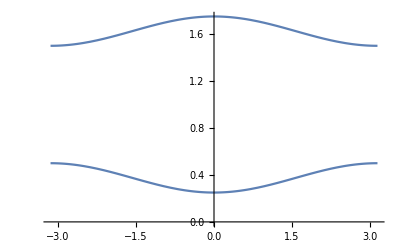

```mathematica
Plot[{eg1,eg2}/.t->0.25,{k,-Pi,Pi}]
```